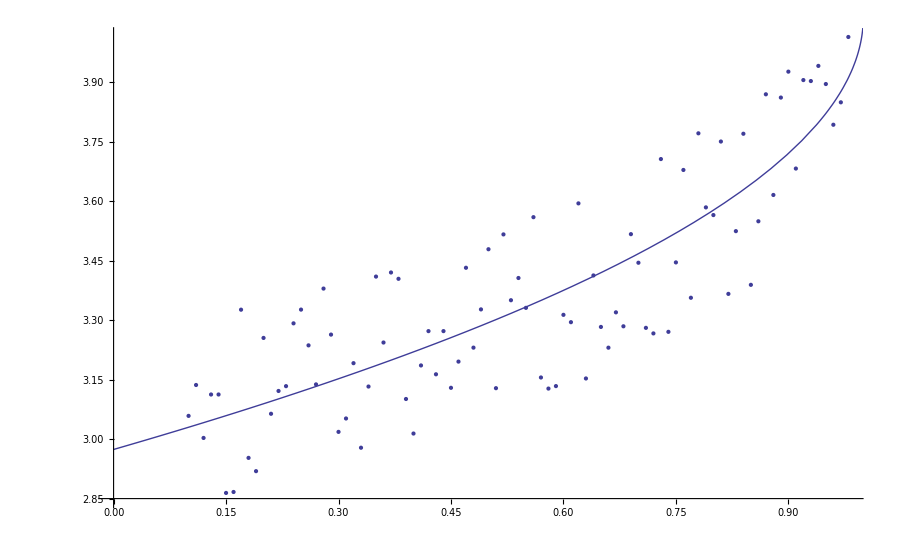

```mathematica
f[t_]:=4.06555364570398+-1.09163397626735*(1-t)^0.5
Show[ListPlot[{{0.1,3.05861571224551},{0.11,3.13651836391851},{0.12,3.00298315071622},{0.13,3.11255450769081},{0.14,3.11258859401718},{0.15,2.8642826008758},{0.16,2.86666264520269},{0.17,3.32646601844917},{0.18,2.95269743798254},{0.19,2.9192078790484},{0.2,3.25523833273946},{0.21,3.06392419201309},{0.22,3.12146119536185},{0.23,3.13358604018129},{0.24,3.29201181466048},{0.25,3.32667604208133},{0.26,3.23646326166185},{0.27,3.13804250447565},{0.28,3.37970444978802},{0.29,3.26364447037072},{0.3,3.01828290670541},{0.31,3.05206304581948},{0.32,3.19156099565701},{0.33,2.97831500017834},{0.34,3.13263673648567},{0.35,3.40997134355034},{0.36,3.2436519350827},{0.37,3.42028743788054},{0.38,3.40434318737843},{0.39,3.10121086498329},{0.4,3.01409174061722},{0.41,3.1858416067244},{0.42,3.27239056216175},{0.43,3.16352680031368},{0.44,3.27241790847278},{0.45,3.12942148069153},{0.46,3.19552596360873},{0.47,3.43219125206717},{0.48,3.23073857323497},{0.49,3.32719697729942},{0.5,3.47893002719992},{0.51,3.12848983843741},{0.52,3.51632194884839},{0.53,3.35033667167471},{0.54,3.40639390234112},{0.55,3.33108783792832},{0.56,3.55980401984658},{0.57,3.15545194511806},{0.58,3.12750171211068},{0.59,3.13372901194919},{0.6,3.31347739769447},{0.61,3.29495821443113},{0.62,3.59459101030287},{0.63,3.15298394261068},{0.64,3.41281157753561},{0.65,3.28296559987478},{0.66,3.23063916685909},{0.67,3.31975976066152},{0.68,3.28456641110118},{0.690000000000001,3.51697688890355},{0.700000000000001,3.44486255401722},{0.710000000000001,3.28064847228049},{0.720000000000001,3.26661513937107},{0.730000000000001,3.70638487695167},{0.740000000000001,3.27061751783042},{0.750000000000001,3.44570934222811},{0.760000000000001,3.67887781243988},{0.770000000000001,3.35654388582261},{0.780000000000001,3.77129151711059},{0.790000000000001,3.58449270447193},{0.800000000000001,3.56511496392213},{0.810000000000001,3.75060365301682},{0.820000000000001,3.3663299819677},{0.830000000000001,3.5245822044964},{0.840000000000001,3.7702226393019},{0.850000000000001,3.38915476018134},{0.860000000000001,3.54941742155796},{0.870000000000001,3.86972486151933},{0.880000000000001,3.61581321519816},{0.890000000000001,3.86146986673547},{0.900000000000001,3.9268403744457},{0.910000000000001,3.68245613753444},{0.920000000000001,3.90559433677384},{0.930000000000001,3.90312740798068},{0.940000000000001,3.94135392856749},{0.950000000000001,3.89562359783776},{0.960000000000001,3.79292377091149},{0.970000000000001,3.84950259635075},{0.980000000000001,4.01427731006783}}],Plot[f[t],{t,0,1}]]
```

```mathematica
f0[x_]:=1;
f1[x_]:=(tc-x)^m;
f2[x_]:=(tc-x)^m Cos[omega *Log[tc-x] ];
f3[x_]:=(tc-x)^m Sin[omega *Log[tc-x] ];
```

```mathematica
D[f1[x],m]
D[f1[x],omega]
D[f1[x],tc]
```

(tc-x)^m Log[tc-x]

0

m (tc-x)^(-1+m)

```mathematica
D[f2[x],m]
D[f2[x],omega]
D[f2[x],tc]
```

(tc-x)^m Cos[omega Log[tc-x]] Log[tc-x]

-(tc-x)^m Log[tc-x] Sin[omega Log[tc-x]]

m (tc-x)^(-1+m) Cos[omega Log[tc-x]]-omega (tc-x)^(-1+m) Sin[omega Log[tc-x]]

```mathematica
D[f3[x],m]
D[f3[x],omega]
D[f3[x],tc]
```

(tc-x)^m Log[tc-x] Sin[omega Log[tc-x]]

(tc-x)^m Cos[omega Log[tc-x]] Log[tc-x]

omega (tc-x)^(-1+m) Cos[omega Log[tc-x]]+m (tc-x)^(-1+m) Sin[omega Log[tc-x]]

```mathematica
f[t_]:= A+t^m * (B+C1*Cos[omega *Log[t] ]+C2*Sin[omega*Log[t]]);
Simplify[D[f[t],t]]
```

t^(-1+m) (B m+(C1 m+C2 omega) Cos[omega Log[t]]+(C2 m-C1 omega) Sin[omega Log[t]])